```mathematica
filenames={
"Table_Deterministic_R_allele_fixation_time_cycle_length.txt",
"Table_Stochastic_EscapeTime_EscapeNumber_cycle_length.txt"
};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../Data/"<>filenames⟦i⟧,"CSV"],{i,Length[filenames]}];
```

## Plot

```mathematica
sorted=GatherBy[data⟦1⟧⟦2;;,{3,4,1}⟧,Last]
```

{{{15,16,0},{13,16,0},{13,17,0},{11,16,0},{12,18,0},{13,20,0},{7,14,0},{7,15,0},{7,16,0},{7,17,0}},{{13,14,1},{13,15,1},{13,17,1},{11,15,1},{11,17,1},{13,19,1},{7,14,1},{7,15,1},{7,16,1},{7,17,1}}}


```mathematica
ListPlot[{
sorted⟦1,All,1⟧,sorted⟦1,All,2⟧,
sorted⟦2,All,1⟧,sorted⟦2,All,2⟧},Joined->True,Frame->True,PlotMarkers->{{-Graphics-,0.02},{-Graphics-,0.02},{-Graphics-,0.02},{-Graphics-,0.02}},PlotStyle->{Black,Gray,Directive[Dashed,Black],Directive[Dashed,Gray]},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015]],PlotRange->{{0.5,10.5},Full}]
```

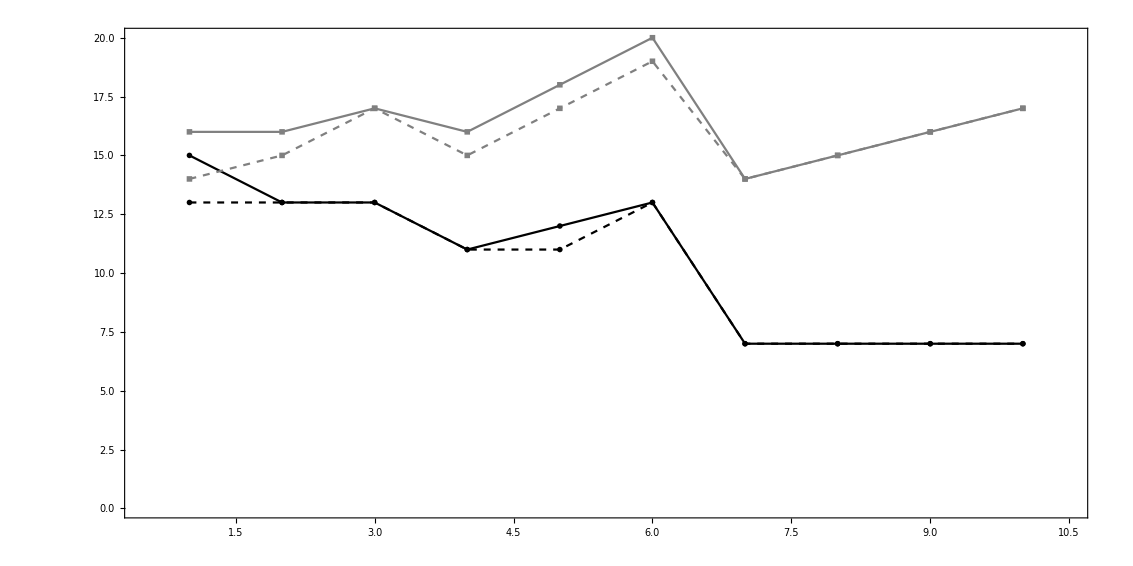

```mathematica
sorted=GatherBy[data⟦2⟧⟦2;;,{4,3,1}⟧,Last]
```

{{{0.18723,15.8799,0},{0.18727,15.9067,0},{0.18876,15.8584,0},{0.18623,15.7414,0},{0.18103,15.5775,0},{0.1801,15.6379,0},{0.17821,15.2823,0},{0.18011,15.4375,0},{0.17964,15.1692,0},{0.18393,15.4223,0}},{{0.07343,11.2737,1},{0.07286,11.3891,1},{0.07019,11.276,1},{0.07195,11.174,1},{0.06838,10.7818,1},{0.06805,10.7809,1},{0.06743,10.6945,1},{0.06838,10.6056,1},{0.06801,10.2301,1},{0.06903,10.4308,1}}}

```mathematica
sorted⟦1,All,1⟧
```

{0.18723,0.18727,0.18876,0.18623,0.18103,0.1801,0.17821,0.18011,0.17964,0.18393}

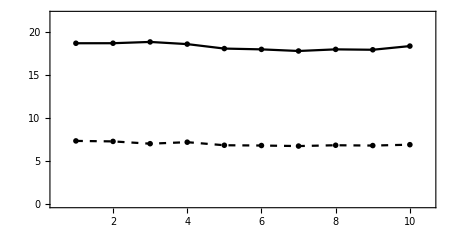

```mathematica
ListPlot[100 {
sorted⟦1,All,1⟧,sorted⟦2,All,1⟧},Joined->True,Frame->True,PlotMarkers->{-Graphics-,0.03},PlotStyle->{Black,Directive[Dashed,Black]},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015]],PlotRange->{{0.5,10.5},{0,22}}]
```

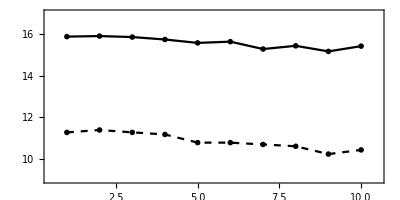

```mathematica
ListPlot[ {
sorted⟦1,All,2⟧,sorted⟦2,All,2⟧},Joined->True,Frame->True,PlotMarkers->{-Graphics-,0.03},PlotStyle->{Black,Directive[Dashed,Black]},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015]],PlotRange->{{0.5,10.5},{9,17}}]
```